# Mathematica as a Tool for Astronomy and Physics

## Lecture 12 Wintersemester 2009/10 Markus Röllig

## Algebra

Required Reading

Formula Manipulation
Polynomial Algebra
Manipulating Equations and Inequalities

### Manipulation of algebraic expressions

Together[expr] puts terms in a sum over a common denominator, and cancels factors in the result.

```mathematica
Together[a/b+c/d]
```

(b c+a d)/(b d)

```mathematica
Together[1/x+1/(x+1)+1/(x+2)+1/(x+3)]
```

(2 (3+11 x+9 x^2+2 x^3))/(x (1+x) (2+x) (3+x))

Apart[expr]rewrites a rational expression as a sum of terms with minimal denominators.

```mathematica
Apart[%]
```

1/x+1/(1+x)+1/(2+x)+1/(3+x)

```mathematica
Apart[(x+y)/((x+1)(y+1)(x-y))]
```

(-1+x)/((1+x)^2 (1+y))-(2 x)/((1+x)^2 (-x+y))

Apart threads over equations and inequalities:

```mathematica
Apart[1<(x+1)/(x-1)<2]
```

1<1+2/(-1+x)<2

Cancel[expr]cancels out common factors in the numerator and denominator of expr.

```mathematica
Cancel[(x^2-1)/(x-1)]
```

1+x

To extract Numerator and Denominator use:

```mathematica
Numerator[ (a b^-2 g^-n)/((c-d)(e-f)^-1)]
```

a (e-f)

```mathematica
Denominator[ (a b^-2 g^-n)/((c-d)(e-f)^-1)]
```

b^2 (c-d) g^n

```mathematica
Denominator[{Sin[x],Cos[x],Tan[x],Csc[x],Sec[x],Cot[x]},Trig->True]
```

{1,1,Cos[x],Sin[x],Cos[x],Sin[x]}

ExpandNumerator expands numerators, ExpandDenominator expands denominators :)

```mathematica
ExpandNumerator[((a+b)(b-2a))/((a-b)a)]
```

(-2 a^2-a b+b^2)/(a (a-b))

```mathematica
ExpandDenominator[((a+b)(b-2a))/((a-b)a)]
```

((-2 a+b) (a+b))/(a^2-a b)

Expand expands numerators leaving denominators in factored form, cancelling common factors where possible.

```mathematica
Expand[((a+b)(b-2a))/((a-b)a)]
```

-(2 a)/(a-b)-b/(a-b)+b^2/(a (a-b))

ExpandAll expands both numerators and denominators.  Note that common factors are not cancelled.

```mathematica
ExpandAll[((a+b)(b-2a))/((a-b)a)]
```

-(2 a^2)/(a^2-a b)-(a b)/(a^2-a b)+b^2/(a^2-a b)

The opposite command is Factor, which reduces an expression to a product of factors.

```mathematica
(a+b)(2a-b)(c-a)(d+b) //Expand
```

-2 a^3 b-a^2 b^2+a b^3+2 a^2 b c+a b^2 c-b^3 c-2 a^3 d-a^2 b d+a b^2 d+2 a^2 c d+a b c d-b^2 c d

```mathematica
Factor[%]
```

-(2 a-b) (a+b) (a-c) (b+d)

```mathematica
((a+b)(2a-b))/((c-a)(d+b)) //ExpandAll
```

(2 a^2)/(-a b+b c-a d+c d)+(a b)/(-a b+b c-a d+c d)-b^2/(-a b+b c-a d+c d)

```mathematica
%//Factor
```

-((2 a-b) (a+b))/((a-c) (b+d))

With the option Trig→True multiple-angle formulae are used to factor expressions involving trigonometric and hyperbolic functions.

```mathematica
Factor[Sin[2x] Cos[2x],Trig->True]
```

2 Cos[x] (Cos[x]-Sin[x]) Sin[x] (Cos[x]+Sin[x])

FunctionExpand[expr]tries to expand out special and certain other functions in expr, when possible reducing compound arguments to simpler ones.

```mathematica
FunctionExpand[Sin[24Degree]]
```

-1/8 √3 (-1-√5)-1/4 √(1/2 (5-√5))

```mathematica
FunctionExpand[{Degree,GoldenRatio}]
```

{π/180,1/2 (1+√5)}

```mathematica
FunctionExpand[HypergeometricPFQ[{1/2},{1,1},z]]
```

BesselI[0,√z]^2

As an example application we can rewrite a solution returned by DSolve:

```mathematica
DSolve[z w'''[z]+2 w''[z]+z w'[z]==0,w[z],z]
```

{{w[z]→C[3]+1/2 (2 C[1] ExpIntegralEi[-ⅈ z]-ⅈ C[2] ExpIntegralEi[ⅈ z])}}

```mathematica
FunctionExpand[w[z]/.%]
```

{C[3]+1/2 (2 C[1] (CosIntegral[z]+1/2 (-Log[ⅈ/z]+Log[-ⅈ z])-Log[z]-ⅈ SinIntegral[z])-ⅈ C[2] (CosIntegral[z]+1/2 (-Log[-ⅈ/z]+Log[ⅈ z])-Log[z]+ⅈ SinIntegral[z]))}

Collect[expr,x] collects together terms involving the same powers of objects matching x.

```mathematica
Collect[a x+b y+c x,x]
```

(a+c) x+b y

```mathematica
Collect[(1+a+x)^4,x]
```

1+4 a+6 a^2+4 a^3+a^4+(4+12 a+12 a^2+4 a^3) x+(6+12 a+6 a^2) x^2+(4+4 a) x^3+x^4

Collect with respect to two variables:

```mathematica
Collect[(x+y+z+1)^4,{x,y}]
```

1+x^4+y^4+4 z+6 z^2+4 z^3+z^4+y^3 (4+4 z)+x^3 (4+4 y+4 z)+y^2 (6+12 z+6 z^2)+y (4+12 z+12 z^2+4 z^3)+x^2 (6+6 y^2+12 z+6 z^2+y (12+12 z))+x (4+4 y^3+12 z+12 z^2+4 z^3+y^2 (12+12 z)+y (12+24 z+12 z^2))

#### Excercises

Combine: x/(1-x^2)-1/(1+x)

Factor:-24 x+12 x^2-24 y+4 x y+10 x^2 y-3 x^3 y-8 y^2+10 x y^2-x^2 y^2-x^3 y^2+2 x y^3-x^2 y^3

Factor: 
a) Cos[x]+Cos[y]	b) Cosh[x]+Cosh[y]

Let expr = Nest[μ #(1-#)&,x,4].
a) Use Collect to produce an explicit polynomial in μ and to factor the coefficients.
b) Alternatively, use CoefficientList to list the coefficients of μ^n and then factor those coefficients.

### Manipulation of trigonometric expressions

Required Reading

Trigonometric Expressions

Many functions are also available for manipulation of expressions involving trigonometric functions, often appearing as counterparts to functions that transform algebraic expressions in similar ways.  Both circular and hyperbolic trigonometry are handled by these functions.  In addition, there are functions which transform between trigonometric and exponential representations.

```mathematica
Expand[Cos[2x] Sin[2x]]
```

Cos[2 x] Sin[2 x]

```mathematica
TrigExpand[Cos[2x] Sin[2x]]
```

2 Cos[x]^3 Sin[x]-2 Cos[x] Sin[x]^3

```mathematica
TrigFactor[2 Cosh[x]^3 Sinh[x]+2 Cosh[x] Sinh[x]^3]
```

2 Cosh[x] (Cosh[x]-ⅈ Sinh[x]) (Cosh[x]+ⅈ Sinh[x]) Sinh[x]

TrigReduce uses trigonometric identities to simplify expressions, generally attempting to reduce the number of trigonometric functions involved, often using multiple-angle formulas.

```mathematica
Sin[x]^3+Cos[x]^3
```

Cos[x]^3+Sin[x]^3

```mathematica
TrigReduce[Sin[x]^5+Cos[x]^4+Tan[x]^3]
```

1/16 (6+8 Cos[2 x]+2 Cos[4 x]+10 Sin[x]-5 Sin[3 x]-4 Sec[x]^3 Sin[3 x]+Sin[5 x]+12 Sec[x]^2 Tan[x])

TrigToExp and ExpToTrig convert between trigonometric and exponential forms.

```mathematica
Cosh[2x]^2 - Sinh[x] //TrigToExp
```

1/2+ⅇ^(-4 x)/4+ⅇ^-x/2-ⅇ^x/2+ⅇ^(4 x)/4

```mathematica
ExpToTrig[%]
```

1/2+1/2 Cosh[4 x]-Sinh[x]

```mathematica
∑_(m=-j)^j Exp[(m y)/j]//ExpToTrig//TrigFactor
```

-Csch[y/(2 j)] Sinh[y/(2 j)-((1+j) y)/j]

#### Excercise

Expand:
a) Cos[4x]	b) Tanh[2x]

Simplify using TrigReduce: 2(cosh(x))^3 sinh(x)+2cosh(x)(sinh(x))^3.

Expand and place over common denominator: 
a) cos(x+y)		b) tanh(x-y)

Use ExpToTrig and TrigFactor to simplify (1+ⅇ^x)/(1-ⅇ^x).  Compare with the effect of Simplify.

### Simplify

Required Reading

Simplification
Simplifying Algebraic Expressions
Simplifying with Assumptions

Perhaps the most useful, but often the most frustrating, Mathematica function for manipulation of symbolic expressions is Simplify, which attempts to reduce an expression to a simpler form.  Simplify includes expansion, factorization, and many other algebraic transformations.  With the option Trig→True, which is the default, it applies trigonometric identities also.  Thus, because Simplify includes all of the functions described above, plus others, the first step in simplifying an expression is usually to append a simplification command in postfix notation, namely expr//Simplify, and seeing what you get.

```mathematica
(4 (Cosh[x]^6 Sinh[x]^2+2 Cosh[x]^4 Sinh[x]^4+Cosh[x]^2 Sinh[x]^6))/(8+12 x+6 x^2+x^3) //Simplify
```

Sinh[4 x]^2/(4 (2+x)^3)

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

```mathematica
Simplify[3/(x+3)+x/(x+3)]
```

1

```mathematica
Simplify[(E^x-E^-x)/Sinh[x]]
```

2

Simplify an equation:

```mathematica
Simplify[2x-4y+6z-10==-8]
```

x+3 z==1+2 y

Simplify does not, however, do more sophisticated transformations that involve, for example, special functions.

```mathematica
Simplify[Gamma[1+n]/n]
```

Gamma[1+n]/n

FullSimplify does perform such transformations.

```mathematica
FullSimplify[Gamma[1+n]/n]
```

Gamma[n]

#### Excercise

Simplify: 
a) 3sin(x)-sin(3x)		b) cos(sin^-1(x)) 	c) (3tanh(x)+tanh^3(x))/(1+3tanh^2(x))

For the expression 2 cosh^3(x) sinh(x) + 2 cosh(x) sinh^3(x), compare the following transformations:
a) Factor	b) Factor[expr,Trig→True]	c) TrigFactor	
d) TrigReduce	e) Simplify	f) Simplify[expr,Trig→False]

Express ln((x+1)/(x-1)) in terms of hyperbolic trigonometric functions.  [Hint: you might need the substitution x→E^(2y) and several steps.]   I leave it to you to judge which form is simplest — most statistical physics textbooks express this formula in terms of hyperbolic trigonometric functions, but rational expressions are pretty simple also.  Often one's preference depends upon context.

Use the following function on Sinh[ArcCosh[x]/2]
a) Simplify	b)FunctionExpand

Simplify: Tan[ArcCos[x]/2]

### Simplification with assumptions

Required Reading

Assumptions and Domains
Using Assumptions

The syntax Simplify[expression,assumptions] permits a list of assumptions to be employed during the simplification of expression.  The assumptions are specified either as a list, {assumption1,assumption2,⋯} or as a logical expression, such as assumption1&&assumption2&&assumption3.  Assumptions can specify the type (domain) for various variables, allowed ranges for values, or relationships between variables.  Assumptions can be employed with Simplify, FullSimplify, FunctionExpand, Refine, Limit, or Integrate.

```mathematica
Simplify[Log[a-b]+Log[a+b]]
```

Log[a-b]+Log[a+b]

Simplification is ineffective without further information about a and b, but if we know that a>b

```mathematica
Simplify[Log[a-b]+Log[a+b],{a>b}]
```

Log[a^2-b^2]

then the two functions can be combined.  Note that the assumption a>b implicitly contains the additional assumption that both a and b are real numbers, so that their magnitudes can be compared directly.  Similarly, the following expressions can be simplified by employing inequalities to define ranges.

```mathematica
Simplify[√(a^2)]
```

√(a^2)

```mathematica
Simplify[√(a^2),a>0]
```

a

```mathematica
Simplify[2 √(x y)≤x+y,{x≥0,y≥0}]
```

True

Without making assumptions about x and y, nothing can be done.

```mathematica
FunctionExpand[Log[x y]]
```

Log[x y]

If x and y are both assumed positive, the log can be expanded.

```mathematica
FunctionExpand[Log[x y],x>0&&y>0]
```

Log[x]+Log[y]

Without making assumptions about x the truth or falsity of this equation cannot be determined.

```mathematica
Simplify[Abs[x]==x]
```

x==Abs[x]

Now Simplify can prove that the equation is true.

```mathematica
Simplify[Abs[x]==x,x>0]
```

True

This proves that erf(x) lies in the range (0,1) for all positive arguments.

```mathematica
FullSimplify[0<Erf[x]<1,x>0]
```

True

Another way to make certain assumptions is Assumptions, which is an option for functions such as Simplify, Refine and Integrate which specifies default assumptions to be made about symbolic quantities.

```mathematica
Limit[Exp[x y],y->∞,Assumptions->{x<0}]
```

0

```mathematica
Simplify[Cos[k Pi]^m,Assumptions->Element[k,Integers]&&Mod[m,2]==0]
```

1

```mathematica
Integrate[x^a,{x,0,1},Assumptions->a>0]
```

1/(1+a)

In something like Simplify[expr,assum] or Refine[expr,assum] you explicitly give the assumptions you want to use. But sometimes you may want to specify one set of assumptions to use in a whole collection of operations. You can do this by using Assuming.

```mathematica
Assuming[x>0,Simplify[Sqrt[x^2]]]
```

x

```mathematica
Assuming[n>0,1+Integrate[x^n,{x,0,1}]^2]
```

1+1/(1+n)^2

Often it is sufficient to specify a domain (Integers, Rationals, Reals, Algebraics, Complexes, Booleans, Primes) for one or more variables.  The function Element[x,domain] specifies that x∈domain is an element of the specified domain.  The element operator ∈ can be entered with the keystroke sequence EscelemEsc.  The variations {x,y,z}∈domain or (x|y|z)∈domain assign each member of a list to the specified domain.  Domains can also be specified for patterns according to patt∈domain.

```mathematica
Simplify[Cos[n π]]
```

Cos[n π]

```mathematica
Simplify[Cos[n π],{n∈Integers}]
```

(-1)^n

```mathematica
Simplify[Cos[n π],{(n+1)/2∈Integers}]
```

-1

A related function is Refine, which uses assumptions to produce output that more closely approximates the form that you might use when its symbols satisfy explicit numerical assumptions.  The result is often better than produced by Simplify, or at least more specific.

```mathematica
Simplify[Abs[x], x < 0] 
Refine[Abs[x], x < 0]
```

Abs[x]

-x

```mathematica
Simplify[Log[x],x<0]
Refine[Log[x],x<0]
```

Log[x]

ⅈ π+Log[-x]

```mathematica
Simplify[Cos[x+πy],y∈Integers]
Refine[Cos[x+πy],y∈Integers]
```

Cos[x+π y]

(-1)^y Cos[x]

This establishes the theorem cosh(x)≥1 if x is assumed to be a real number.

```mathematica
Simplify[Cosh[x]>=1,x ∈ Reals]
```

True

#### Excercises

Under what assumptions will (x^m)^n reduce to x^(m n)?  Verify.  List a few examples which show that uncritical use of the proposed replacement rule leads to incorrect results.

Prove a^n-b^n=(a-b)(a^(n-1)+a^(n-2)b + ⋯+ b^(n-1)) for any positive integer n and real a,b.

### Manual manipulation of expressions

Sometimes, you might want to rearrange expressions to your liking, e.g. by adding something to both sides of an equation or by dividing by a some constant (non-zero) factor. One way to do this is by using Apply.

Imagine the equation of motion for a simple spring pendulum

```mathematica
eq=m x''[t]+(m g)/l x[t]==0
```

(g m x[t])/l+m x''[t]==0

Since physically, m>0 we can get rid of it by dividing eq by m. However, the following does not work

```mathematica
eq/m//FullSimplify
```

(m ((g x[t])/l+x''[t])==0)/m

We need to do it for the lhs and rhs seperately.

```mathematica
(#/m)&/@eq//FullSimplify
```

(g x[t])/l+x''[t]==0

Another possibility is the command Thread

```mathematica
Thread[eq/m,Equal]//FullSimplify
```

(g x[t])/l+x''[t]==0

### Symbolic Solution of Equations

Required Reading

Symbolic Calculations
Solving Equations
Simultaneous Equations
Eliminating Variables
Polynomial Algebra
Algebraic Operations on Polynomials

The basic tools for symbolic solution of algebraic equations are Solve, Reduce, and Eliminate.  Solve[eqs,vars] attempts to solve an equation or list of equations, eqs, for the variable or list of variables, vars.  Equations must be expressed in the form lhs==rhs.

```mathematica
Solve[x^2+a x+1==0,x]
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

Solutions are given as lists of replacements. Pick out the second solution:

```mathematica
Solve[x^2+a x+1==0,x][[2]]
```

{x→1/2 (-a+√(-4+a^2))}

A particular solution can then be selected by using the replacement rule of your choice to make an assignment.

```mathematica
solution=Solve[x^2+a x+1==0,x]
x1=x/.solution[[1]]
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

1/2 (-a-√(-4+a^2))

We can verify the soultion

```mathematica
Simplify[x^2+a x+1==0/.solution]
```

{True,True}

The well known p-q formula

```mathematica
Solve[x^2+p x+q==0,x]//Expand
```

{{x→-p/2-1/2 √(p^2-4 q)},{x→-p/2+1/2 √(p^2-4 q)}}

Solve simultaneous equations in x and y:

```mathematica
Solve[{a x+y==7,b x-y==1},{x,y}]
```

{{x→8/(a+b),y→-(a-7 b)/(a+b)}}

```mathematica
Solve[{x^2+y^2==1,x+y==a},{x,y}]
```

{{x→1/2 (a-√(2-a^2)),y→1/2 (a+√(2-a^2))},{x→a/2+(√(2-a^2))/2,y→1/2 (a-√(2-a^2))}}

When you are working with sets of equations in several variables, it is often convenient to reorganize the equations by eliminating some variables between them.

Eliminate[eqns,vars]eliminates variables between a set of simultaneous equations.

This eliminates y between the two equations, giving a single equation for x.

```mathematica
Eliminate[{a x+y==0,2 x+(1-a) y==1},y]
```

(2-a+a^2) x==1

Example: Rewrite f in terms of a and b:

```mathematica
Eliminate[{f==x^5+y^5,a==x+y,b==x y},{x,y}]
```

f==a^5-5 a^3 b+5 a b^2

If you have several equations, there is no guarantee that there exists any consistent solution for a particular variable.

```mathematica
Solve[{x == 1, x == 2}, x]
```

{}

```mathematica
Solve[{x==1,x==a},x]
```

{}

The general question of whether a set of equations has any consistent solution is quite a subtle one. For example, for most values of a, the equations {x==1,x==a} are inconsistent, so there is no possible solution for x. However, if a is equal to 1, then the equations do have a solution. Solve is set up to give you generic solutions to equations. It discards any solutions that exist only when special constraints between parameters are satisfied.

If you use Reduce instead of Solve, Mathematica will however keep all the possible solutions to a set of equations, including those that require special conditions on parameters.

This shows that the equations have a solution only when a==1. The notation a==1&&x==1 represents the requirement that both a==1 and  x==1 should be True.

```mathematica
Reduce[{x==a,x==1},x]
```

a==1&&x==1

This gives the complete set of possible solutions to the equation. The answer is stated in terms of a combination of simpler equations. && indicates equations that must simultaneously be true; || indicates alternatives.

```mathematica
Reduce[a x-b==0,x]
```

(b==0&&a==0)||(a≠0&&x==b/a)

Mathematica also works on inequalities

```mathematica
Reduce[x^2+y^2<1,{x,y}]
```

-1<x<1&&-√(1-x^2)<y<√(1-x^2)

Example: Find a Pythagorean triple

```mathematica
Reduce[x^2+y^2==5^2&&y>x>0,{x,y},Integers]
```

x==3&&y==4

```mathematica
Clear[solution,x1]
```

In dealing with sets of equations, it is common to consider some of the objects that appear as true "variables", and others as "parameters". In some cases, you may need to know for what values of parameters a particular relation between the variables is always satisfied.

SolveAlways[eqns,vars]gives the values of parameters that make the equations eqns valid for all values of the variables vars. Compare

```mathematica
SolveAlways[a x+b==0,x]
```

{{a→0,b→0}}

```mathematica
Solve[a x+b==0,x]
```

{{x→-b/a}}

This finds the values of parameters that make the equation hold for all x.

```mathematica
SolveAlways[a+b x+c x^2==(1+x)^2,x]
```

{{a→1,b→2,c→1}}

#### Excercise

Use Reduce to find ways of  how to pay $2.27 postage with 10-, 23- and 37-cent stamps

Find a other sets of  of Pythagorean triples than {3,4,5}

Find the roots of LegendreP[6,x] symbolically and verify that these roots are, in fact, real.

Find a set of parameters that make the equation a + b x + c x^2 == (1 + x)^2 hold for all x.

Find values of a and b such that the following is always true:
Series[a Cos[x] + b Cos[2 x] + Cos[3 x], {x, 0, 3}] == Series[Cosh[x], {x, 0, 3}]

### Numerical Equation Solving

Required Reading:

Numerical Equation Solving

An equation or system of equations involving only polynomials can be solved numerically using NSolve[eqs,vars,n] where eqs is an equation or list of equations, vars is the variable or list of variables, and n is an optional parameter specifying the precision sought in terms of number of decimal digits.  The result is returned as a list of sets of replacement rules.

```mathematica
NSolve[x^5-2x+3==0,x]
```

{{x→-1.42361},{x→-0.246729-1.32082 ⅈ},{x→-0.246729+1.32082 ⅈ},{x→0.958532-0.498428 ⅈ},{x→0.958532+0.498428 ⅈ}}

```mathematica
NSolve[{x^2+y^2==1,2x+3y==4},{x,y}]
```

{{x→0.615385+0.399704 ⅈ,y→0.923077-0.266469 ⅈ},{x→0.615385-0.399704 ⅈ,y→0.923077+0.266469 ⅈ}}

```mathematica
NSolve[{x+y==2,x-3 y+z==3,x-y+z==0},{x,y,z}]
```

{{x→3.5,y→-1.5,z→-5.}}

If your equations involve only linear functions or polynomials, then you can use NSolve to get numerical approximations to all the solutions. However, when your equations involve more complicated functions, there is in general no systematic procedure for finding all solutions, even numerically. In such cases, you can use FindRoot to search for solutions. You have to give FindRoot a place to start its search.

This searches for a numerical solution, starting at x=1.

```mathematica
FindRoot[3 Cos[x]==Log[x],{x,1}]
```

{x→1.44726}

When solving a polynomial equation of degree less than 5. Mathematica can always solve such an equation exactly using radicals, that is, only using the operations of addition, subtraction, multiplication, division, and taking roots.

```mathematica
Solve [x^4-2 x^3+x+5==0,x]
```

{{x→1/2 (1-√(3-2 ⅈ √19))},{x→1/2 (1+√(3-2 ⅈ √19))},{x→1/2 (1-√(3+2 ⅈ √19))},{x→1/2 (1+√(3+2 ⅈ √19))}}

But, as a consequence of Galois theory this is not possible in general for polynomial equations of degree 5 or more. It might be possible in special cases, but no general formula (like the famous quadratic formula in the degree two case) can exist.

```mathematica
Solve[x^5-2 x^3+x+5==0,x]
```

{{x→Root[5+#1-2 #1^3+#1^5&,1]},{x→Root[5+#1-2 #1^3+#1^5&,2]},{x→Root[5+#1-2 #1^3+#1^5&,3]},{x→Root[5+#1-2 #1^3+#1^5&,4]},{x→Root[5+#1-2 #1^3+#1^5&,5]}}

Mathematica knows that a polynomial of degree 5 has 5 roots. But it can not give you the roots symbolically. The expression  Root[5+#1-2 #1^3+#1^5&,3] is just the general name of the third root of the above polynomial. If you want to know the roots, you have to calculate them numericall:

```mathematica
NSolve[x^5-2 x^3+x+5==0,x]
```

{{x→-1.65477},{x→-0.527822-1.02701 ⅈ},{x→-0.527822+1.02701 ⅈ},{x→1.35521-0.655415 ⅈ},{x→1.35521+0.655415 ⅈ}}

If you use approximate numbers instead of exact numbers, Mathematica will also switch to numerical solutions:

```mathematica
Solve[x^5-2.0 x^3+x+5==0,x]
```

{{x→-1.65477},{x→-0.527822-1.02701 ⅈ},{x→-0.527822+1.02701 ⅈ},{x→1.35521-0.655415 ⅈ},{x→1.35521+0.655415 ⅈ}}

NSolve also solves polynomial equations in several variables. Here is a series of equations.

```mathematica
equations[var_] := Table[Sum[(-1)^i x[i]^j, {i, var}] == j^2, {j, var}]
```

```mathematica
equations[4]//TableForm
```

-x[1]+x[2]-x[3]+x[4]==1
-x[1]^2+x[2]^2-x[3]^2+x[4]^2==4
-x[1]^3+x[2]^3-x[3]^3+x[4]^3==9
-x[1]^4+x[2]^4-x[3]^4+x[4]^4==16

```mathematica
NSolve[equations[4], Table[x[i], {i, 4}]] // Timing
```

{0.016,{{x[1]→0.826923+0.793915 ⅈ,x[2]→0.785835,x[3]→0.826923-0.793915 ⅈ,x[4]→1.86801},{x[1]→0.826923-0.793915 ⅈ,x[2]→0.785835,x[3]→0.826923+0.793915 ⅈ,x[4]→1.86801},{x[1]→0.826923+0.793915 ⅈ,x[2]→1.86801,x[3]→0.826923-0.793915 ⅈ,x[4]→0.785835},{x[1]→0.826923-0.793915 ⅈ,x[2]→1.86801,x[3]→0.826923+0.793915 ⅈ,x[4]→0.785835}}}

Typically, the running time of NSolve increases rapidly with the number of equations and their degree:

```mathematica
Table[{ξ, Timing[NSolve[equations[ξ], Table[x[i], {i, ξ}]]][[1]]}, 
      {ξ, 6}](* don't use ξ larger than 7 *)
```

{{1,0.},{2,0.016},{3,0.},{4,0.016},{5,0.062},{6,0.297}}

Mathematica also solves multivariate cases, which are non-trivial to solve.

```mathematica
NSolve[{
x^6 y^8 - x^8 y^6 == 1, 
x^5 y^7 - x^7 y^5 == 1
}, {x, y},
WorkingPrecision->60]
```

{{x→1.2720196495140689642524224617374914917156080418400962486166 ⅈ,y→-0.7861513777574232860695585858429589295231220578377232376649 ⅈ},{x→-1.2720196495140689642524224617374914917156080418400962486166 ⅈ,y→0.7861513777574232860695585858429589295231220578377232376649 ⅈ},{x→0.7861513777574232860695585858429589295231220578377232376649,y→1.2720196495140689642524224617374914917156080418400962486166},{x→-0.7861513777574232860695585858429589295231220578377232376649,y→-1.2720196495140689642524224617374914917156080418400962486166}}

#### Excercise

Write a function using NSolve and Cases which returns the real solutions to  the following equation in terms of the parameter a :
		2==r^4+(a r^4)/(1+r)^4

Plot these solutions for {a,-1,1}.  [Hint: it is probably easiest to use ListPlot for this purpose.]

Find intersection points of a unit circle centered at {0,0} and a parabola. (Hint: parabola equation y - 2 x^2 + 3/2 == 0)

Find the first 3 positive roots of tan(x)=1/x.

Find the first 3 positive roots of BesselJ[2,x].  Then explore the sensitivity to starting values; for example, compare results for starting points of 6.8, 7.0, 7.2.

Find all real solutions to the pair of equations x^4+y^4=1 and e^x-e^y= 1.  [Hint: use ImplicitPlot to display the two equations and to locate appropriate starting values.]

### Systems of Linear Equations

Required Reading

Solving Linear Systems
Linear Systems

Of course Solve also works on linear equations.

```mathematica
Solve [{3 x+2 y-z+w==0,x-3 z==-1,-y+w==2},{x,y,z}]
```

{{x→1/8 (13-9 w),y→-2+w,z→1/8 (7-3 w)}}

However, while the above example solves our problem, it is better to take the point of
linear algebra and view the system of equations in terms of the following matrix
equation.

(3 | 2 | -1 | 1
1 | 0 | -3 | 0
0 | -1 | 0 | 1)(x
y
z
w)=(0
-1
2)

Mathematica uses many very well optimized methods for solvinf linear systems of the form A x=b.

LinearSolve[m,b]finds an x which solves the matrix equation m.x==b.

```mathematica
LinearSolve[{{3,2,-1,1},{1,0,-3,0},{0,-1,0,1}},{0,-1,2}]
```

{13/8,-2,7/8,0}

Attention, Mathematica gives the single solution corresponding to w=0! If you have a square matrix m with a nonzero determinant, then you can always find a unique solution to the matrix equation m.x=b for any b. If, however, the matrix m has determinant zero, then there may be either no vector, or an infinite number of vectors x which satisfy m.x=b for a particular b. This occurs when the linear equations embodied in m are not independent.

When m has determinant zero (or no determinant), it is nevertheless always possible to find nonzero vectors x that satisfy m.x=0. The set of vectors x satisfying this equation form the null space or kernel of the matrix m. Any of these vectors can be expressed as a linear combination of a particular set of basis vectors, which can be obtained using NullSpace[m].

To find all the solutions to Ax = b using LinearSolve we need to also use the Mathematica function NullSpace to find the null space of A.We can then take the single solution given by LinearSolve and add to it any vector in the null space.

```mathematica
NullSpace[{{3,2,-1,1},{1,0,-3,0},{0,-1,0,1}}]
```

{{-9,8,-3,8}}

Mathematica finds that the vector (-9, 8, -3, 8) is in the null space. But, of course, if a vector is in the null space of A, then so is any multiple of it, since A(cx) = cAx. So, in this case, we see that the null space of A is the line consisting of all multiples of (−9, 8,−3, 8). So our set of solutions is

```mathematica
LinearSolve[{{3,2,-1,1},{1,0,-3,0},{0,-1,0,1}},{0,-1,2}]+w NullSpace[{{3,2,-1,1},{1,0,-3,0},{0,-1,0,1}}][[1]]
```

{13/8-9 w,-2+8 w,7/8-3 w,8 w}

### Solving Nonpolynomial Equations

```mathematica
Solve[x^2==Exp[x], x]
Solve[x==Cos[x ], x]
Solve[ Log[x]+Log[2]==1/x, x]
Solve[Sin[2 x] Tan[x]==2 x, x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-2 ProductLog[-1/2]},{x→-2 ProductLog[1/2]}}

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[x==Cos[x],x]

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1/ProductLog[2]}}

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[Sin[2 x] Tan[x]==2 x,x]

Even NSolve is only partially successful

```mathematica
NSolve[x^2==Exp[x], x]
NSolve[x==Cos[x ], x]
NSolve[ Log[x]+Log[2]==1/x, x]
NSolve[Sin[2 x] Tan[x]==2 x, x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.703467},{x→1.58805-1.54022 ⅈ}}

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

NSolve[x==Cos[x],x]

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1.17288}}

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

NSolve[Sin[2 x] Tan[x]==2 x,x]

Solving these equations is equivalent to finding intersection points between the lhs-curve and the rhs-curve.

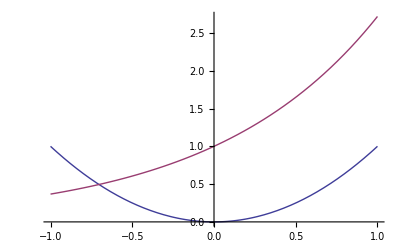

```mathematica
Plot[{x^2,Exp[x]},{x,-1,1}]
```

We will use FindRoot[f,{x,x_0}]to search for a numerical root of f, starting from the point x=x_0.

```mathematica
FindRoot[x^2==Exp[x], {x,-.5}]
```

{x→-0.703467}

It is always helpful to plot lhs and rhs to get an idea of feasible starting points

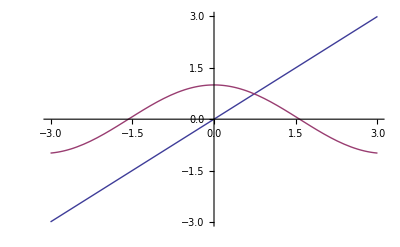

```mathematica
Plot[{x,Cos[x ]},{x,-3,3}]
```

```mathematica
FindRoot[x==Cos[x ],{x,1}]
```

{x→0.739085}

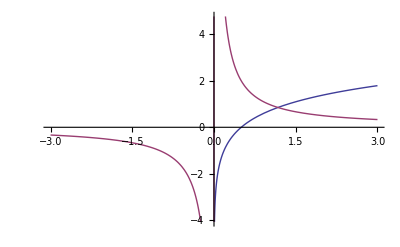

```mathematica
Plot[{Log[x]+Log[2],1/x},{x,-3,3}]
```

```mathematica
FindRoot[ Log[x]+Log[2]==1/x, {x,1}]
```

{x→1.17288}

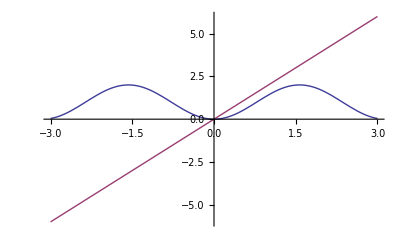

```mathematica
Plot[{Sin[2 x] Tan[x],2 x},{x,-3,3}]
```

FindRoot continues until either of the goals specified by AccuracyGoal or PrecisionGoal is achieved.

```mathematica
FindRoot[Sin[2 x] Tan[x]==2 x, {x,1}]
```

{x→-3.32109×10^-20}

The standard method used by FindRoot is Newton's method. It requires a reasonable initial point:

```mathematica
FindRoot[Sin[2 x] Tan[x]==2 x, {x,0}]
```

{x→0.}

#### Excercises

Find all roots of the equation 1+x^3/100==x Sin[x]

### Excercises

Solve x y + y - 3= (2x+y)/(3x+4)for x in terms of y. Repeat for y in terms of x.

Plot the roots of x^6+x+1.

Find all solutions to the following system of linear equations
		x -z = 4
	2x + y - 3z = 5

Find the intersetioon points of the two curves in polar coordinates:
3/2 Sin[5θ]==1+Cos[5θ]^2

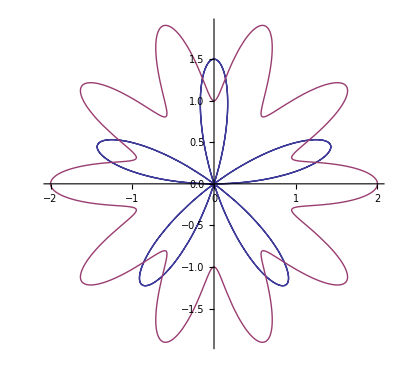

```mathematica
PolarPlot[{3/2 Sin[5θ],1+Cos[5θ]^2},{θ,0,2Pi}]
```

#### Forgotten form of quadratic theorem

Everyone knows that the solutions to the quadratic equation a x^2+b x+c==0 are x=(-b±√(b^2-4a c))/(2a), but there is another form that is sometimes useful for hand calculation.  Prove that the solutions can also be expressed in the form x=(2c)/(∓√(b^2-4a c)-b).

#### Quadratic form in two dimensions

A general two-dimensional quadratic form is represented by the expression a x^2 + b x y + c y^2 + d x + e y + f.  Coordinate transformations can be used to eliminate the linear terms and the cross terms, thereby simplifying the quadratic form in the new coordinate system.
a) A translation of the origin is accomplished by the replacements {x→x-x_0,y→y-y_0}.  Perform this transformation and isolate the coefficient of the linear terms, x and y.  [Note that the desired coefficient of x is independent of y, and vice versa, because we will handle the cross term separately.
b) Determine the values of {a,b} which eliminate the linear terms and produce a transformed expression in the new coordinate system.  [Hint: solve a pair of equations.]
c) A rotation of the coordinate system is accomplished by the replacements {x→x Cos[θ] + y Sin[θ],y→-x Sin[θ]+y Cos[θ]}.  Perform this transformation and isolate the coefficient of the cross term.  Find a set of angles θ for which the cross term is absent in the rotated coordinate system.  Compare the new expressions for each θ solution.

## Piecewise Functions

Required reading:

Piecewise Functions

### Piecewise

Instead of using Which to define a piecewise function, Mathematica offers the command Piecewise[{{val_1,cond_1},{val_2,cond_2},…}], which represents a piecewise function with values val_i in the regions defined by the conditions cond_i.

```mathematica
h[x_]:=Piecewise[{{x^2,x<0},{x,x>0}}]
```

```mathematica
h[x]
```

Piecewise[{{x^2, x<0}, {x, x>0}, {0, True}}]

```mathematica
h[x]//TraditionalForm
```

Piecewise[{{x^2, x<0}, {x, x>0}}]

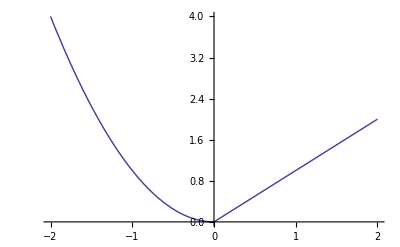

```mathematica
Plot[h[x],{x,-2,2}]
```

Piecewise defined functions can be differentiated

```mathematica
D[h[x],x]
```

Piecewise[{{2 x, x<0}, {1, x>0}, {Indeterminate, True}}]

and integrated

```mathematica
Integrate[h[x],{x,-5,5}]
```

325/6

```mathematica
Integrate[h[x],x]
```

Piecewise[{{x^3/3, x≤0}, {x^2/2, True}}]

To enter the piecewise braces use Esc pwEsc to enter { andCtrl+Comma and then Ctrl+ for each additional piecewise case.

You can solve piecewise differential equations

```mathematica
DSolve[x''[t]+x[t]==Piecewise[{{Sqrt[t],t>0}}],x[t],t]
```

{{x[t]→C[1] Cos[t]+Cos[t] (Piecewise[{{0, t≤0}, {√t Cos[t]-√(π/2) FresnelC[√(2/π) √t], True}}])+C[2] Sin[t]+Piecewise[{{0, t≤0}, {-√(π/2) FresnelS[√(2/π) √t]+√t Sin[t], True}}] Sin[t]}}

An example application is the calculation of the volume of an ellipsoid

```mathematica
Integrate[Piecewise[{{1,x^2/a^2+y^2/b^2+z^2/c^2≤1}}],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->a>0&&b>0&&c>0]
```

4/3 a b c π

Piecewise functions can be combined too

```mathematica
(h[x]+2h[x]-h[x]^2)/(h[x]+h[x]^3)
```

(3 (Piecewise[{{x^2, x<0}, {x, x>0}, {0, True}}])-(Piecewise[{{x^2, x<0}, {x, x>0}, {0, True}}])^2)/(Piecewise[{{x^2, x<0}, {x, x>0}, {0, True}}]+(Piecewise[{{x^2, x<0}, {x, x>0}, {0, True}}])^3)

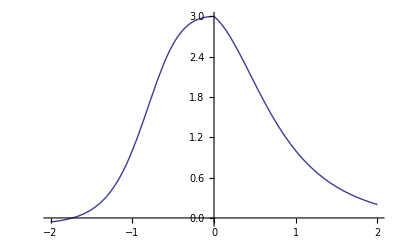

```mathematica
Plot[%,{x,-2,2}]
```

PiecewiseExpand[expr]expands nested piecewise functions in expr to give a single piecewise function.  We make the above example a little more complicated:

```mathematica
(h[x]+2h[x]-h[x-ξ]^2)/(h[x]+h[x]^3)
PiecewiseExpand[(h[x]+2h[x]-h[x-ξ]^2)/(h[x]+h[x]^3)]
```

(3 (Piecewise[{{x^2, x<0}, {x, x>0}, {0, True}}])-(Piecewise[{{(x-ξ)^2, x-ξ<0}, {x-ξ, x-ξ>0}, {0, True}}])^2)/(Piecewise[{{x^2, x<0}, {x, x>0}, {0, True}}]+(Piecewise[{{x^2, x<0}, {x, x>0}, {0, True}}])^3)

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

Piecewise[{{(3 x^2-(x-ξ)^4)/(x^2+x^6), x<0&&x-ξ<0}, {(3 x^2-(x-ξ)^2)/(x^2+x^6), x<0&&x-ξ>0}, {(3 x^2)/(x^2+x^6), x<0}, {(3 x-(x-ξ)^4)/(x+x^3), x-ξ<0&&x>0}, {(3 x-(x-ξ)^2)/(x+x^3), x>0&&x-ξ>0}, {(3 x)/(x+x^3), x>0}, {ComplexInfinity, x>0||x<0||x-ξ>0||x-ξ<0}, {Indeterminate, True}}]

Mathematica implicitely assumes that ξ is real because conditions in the piecewise function contain comparison functions. We can again plot the result, now as function of x and ξ.

```mathematica
Plot3D[Evaluate[%], {x, -3, 3}, {ξ, -3, 3}, PlotPoints ->40]
```

-Graphics3D-

You can also use PiecewiseExpand to expand other expressions:

```mathematica
PiecewiseExpand[Max[a,b,c,d]]
```

Piecewise[{{a, a-b≥0&&a-c≥0&&a-d≥0}, {b, a-b<0&&b-c≥0&&b-d≥0}, {c, a-c<0&&b-c<0&&c-d≥0}, {d, True}}]

```mathematica
PiecewiseExpand/@{KroneckerDelta[x,y],DiscreteDelta[x,y]}
```

{Piecewise[{{1, x-y==0}, {0, True}}],Piecewise[{{1, x==0&&y==0}, {0, True}}]}

Expand assuming real parameters:

```mathematica
PiecewiseExpand[Abs[x],Reals]
```

Piecewise[{{-x, x<0}, {x, True}}]

```mathematica
PiecewiseExpand[Max[Abs[x],Abs[y]],Reals]
```

Piecewise[{{-x, (x<0&&y≥0&&x+y≤0)||(x<0&&y<0&&x-y≤0)}, {x, (x≥0&&x-y≥0&&y≥0)||(x≥0&&y<0&&x+y≥0)}, {-y, (x≥0&&y<0&&x+y<0)||(x<0&&y<0&&x-y>0)}, {y, True}}]

If, Which and Switch can be interpreted as piecewise functions:

```mathematica
PiecewiseExpand/@{If[a,x,y],Which[a,x,b,y,c,z],Switch[u,v,x,w,y]}
```

{Piecewise[{{x, a}, {y, True}}],Piecewise[{{x, a}, {y, !a&&b}, {z, !a&&!b&&c}, {0, True}}],Piecewise[{{x, u-v==0}, {y, u-v≠0&&u-w==0}, {0, True}}]}

Convert SquareWave, TriangleWave and SawtoothWave for finite ranges:

```mathematica
PiecewiseExpand/@{SquareWave[x],TriangleWave[x],SawtoothWave[x]}]
```

### Boole

Boole[expr] is a basic function that turns True and False into 1 and 0. It is sometimes known as the characteristic function or indicator function. Boole[expr]yields 1 if expr is True and 0 if it is False.

```mathematica
{Boole[False],Boole[True]}
```

{0,1}

This gives the area of a unit disk.

```mathematica
Integrate[Boole[x^2+y^2<=1],{x,-1,1},{y,-1,1}]
```

π

Example: Find the area of the intersection of a circle with a parametric radius and a square:

```mathematica
Integrate[Boole[x^2+ y^2<a],{x,-1,1},{y,-1,1}]
```

Piecewise[{{4, a≥2}, {a π, 0<a≤1}, {2 (2 √(-1+a)+a ArcCsc[√a]-a ArcTan[√(-1+a)]), 1<a<2}, {0, True}}]

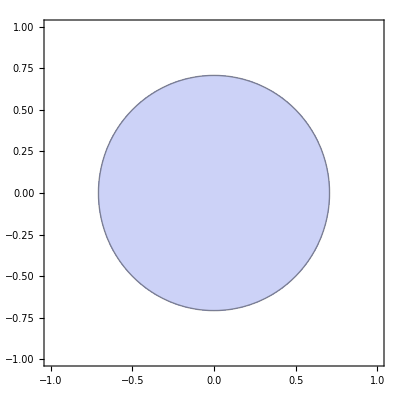
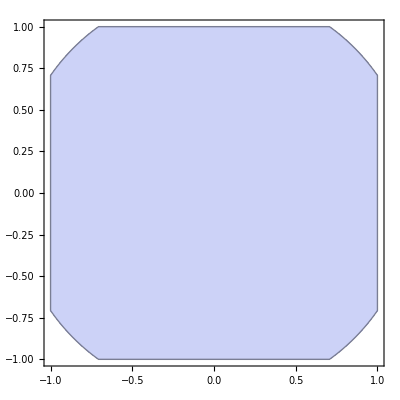
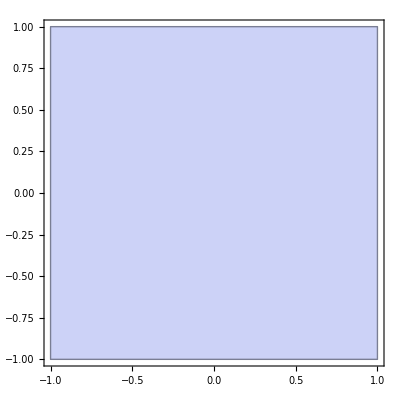

```mathematica
Table[RegionPlot[x^2+ y^2<a,{x,-1,1},{y,-1,1}],{a,{1/2,3/2,5/2}}]
```

Another example from comp.soft-sys.math.mathematica

```mathematica
With[{fJ=3,fH=2,f1=1/2,f2=-4^(-1)},
Print[Plot3D[Boole[x^2+y^2<fJ^2&&(x-f1)^2+y^2<fH^2&&(x-f2)^2+y^2<fH^2]*x^2*y^2,{x,-5,5},{y,-5,5}]];Integrate[Boole[x^2+y^2<fJ^2&&(x-f1)^2+y^2<fH^2&&(x-f2)^2+y^2<fH^2]*x^2*y^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity}]]
```

-Graphics3D-

(-169077 √247+1802240 ArcCos[3/16]+2867200 ArcCsc[4 √(2/13)])/491520

Find the area of a region defined by an inequality:

```mathematica
ineq=y^2-4x^2+4x^4≤0;
```

```mathematica
Integrate[Boole[ineq], {x, -Infinity, Infinity}, {y, -Infinity, Infinity}]
```

8/3

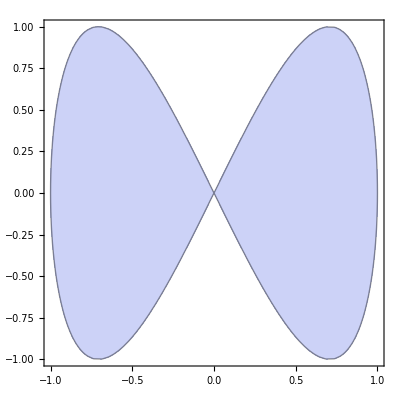

```mathematica
RegionPlot[ineq,{x,-1,1},{y,-1,1}]
```

### Clip

Clip[x] is effectively equivalent to Piecewise[{{-1,x<-1},{+1,x>+1}},x]. Clip[x]gives x clipped to be between -1 and +1.

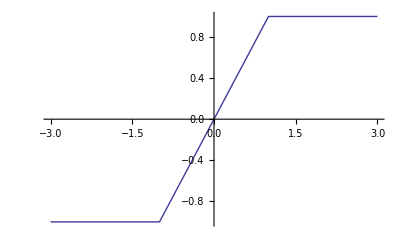

```mathematica
Plot[Clip[x],{x,-3,3}]
```

One can use different clip levels: Clip[x,{min,max}]gives x for min≤x≤max, min for x<min and max for x>max.

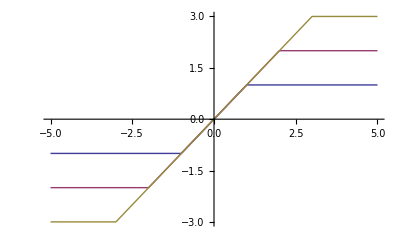

```mathematica
Plot[Evaluate@Table[Clip[x,{-a,a}],{a,3}],{x,-5,5}]
```

Lile all the functions before, Clip works symboliclly and numerically

```mathematica
Integrate[Clip[1/(x-1)],x]
```

Piecewise[{{Log[-1+x], x≤0}, {ⅈ π-x, 0<x≤1}, {-2+ⅈ π+x, 1<x≤2}, {ⅈ π+Log[-1+x], True}}]

```mathematica
Series[Clip[2Sin[x]],{x,0,2}]
```

Piecewise[{{-1, Sin[x]<-1/2}, {1, Sin[x]>1/2}, {2 x+O[x]^3, True}}]

### UnitStep

UnitStep[x]represents the unit step function, equal to 0 for x<0 and 1 for x≥0.

```mathematica
UnitStep[1]
```

1

```mathematica
UnitStep[x]//TraditionalForm
```

x

The differentiation of the distribution θ yields the Dirac δ function.

```mathematica
UnitStep'[x]
```

Piecewise[{{Indeterminate, x==0}, {0, True}}]

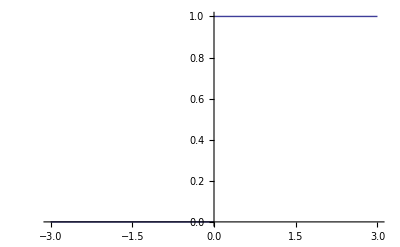

```mathematica
Plot[UnitStep[x],{x,-3,3},PlotStyle->Thick]
```

```mathematica
Plot3D[UnitStep[x,y],{x,-3,3},{y,-3,3},Mesh->5]
```

-Graphics3D-

The integral ∫_0^∞ log(x) (x^3-1)^-1dx can be written as an integral over the domain {-∞,∞} as ∫_(-∞)^∞ θ(x)log(x) (x^3-1)^-1dx. Integrate knows how to deal with this form.

```mathematica
Integrate[Log[x]/(x^3 + 1), {x, 0, Infinity}]
```

-(2 π^2)/27

```mathematica
Integrate[Log[x]/(x^3 + 1) UnitStep[x], {x, -Infinity, Infinity}]
```

-(2 π^2)/27

UnitStep can be used to construct piecewise functions:

```mathematica
PiecewiseExpand[x^2+(x-x^2) UnitStep[x]]
```

Piecewise[{{x, x≥0}, {x^2, True}}]

Generate a square wave:

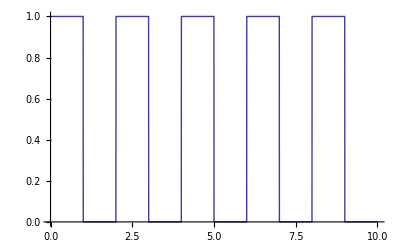

```mathematica
Plot[UnitStep[Sin[Pi x]],{x,0,10},Exclusions->None,PlotStyle->Thick]
```

Use it in differential equations as well:  Compute a step response for a continuous-time system:

```mathematica
DSolve[{y''[t]+y'[t]+y[t]==UnitStep[t],y[0]==y'[0]==0},y,t]
```

{{y→Function[{t},1/3 ⅇ^(-t/2) (3 ⅇ^(t/2)-3 Cos[(√3 t)/2]-√3 Sin[(√3 t)/2]) UnitStep[t]]}}

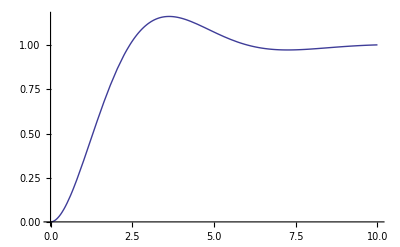

```mathematica
Plot[Evaluate[y[t]/.%],{t,0,10}]
```

Solve the time-independent Schrödinger equation with piecewise analytic potential:

```mathematica
DSolve[{-ψ''[z]+UnitStep[z]ψ[z]==ε ψ[z],ψ[0]==ψ0,ψ'[0]==ψ1},ψ[z],z]
```

{{ψ[z]→(√ε ψ0 Cos[z √ε]+ψ1 Sin[z √ε])/(√ε)+((ⅇ^(-z √(1-ε)) (√(1-ε) ψ0+ⅇ^(2 z √(1-ε)) √(1-ε) ψ0-ψ1+ⅇ^(2 z √(1-ε)) ψ1))/(2 √(1-ε))-(√ε ψ0 Cos[z √ε]+ψ1 Sin[z √ε])/(√ε)) UnitStep[z]}}

You can expand  UnitStep using FunctionExpand

```mathematica
UnitStep[x^2-11x+1]//FunctionExpand
```

UnitStep[1/2 (11-3 √13)-x]+UnitStep[1/2 (-11-3 √13)+x]

and convert into Piecewise:

```mathematica
PiecewiseExpand[UnitStep[x]]
```

Piecewise[{{1, x≥0}, {0, True}}]

```mathematica
PiecewiseExpand[Exp[x UnitStep[x]UnitStep[1-UnitStep[x]]]]
```

Piecewise[{{1, x<0}, {ⅇ^x, True}}]

```mathematica
Integrate[UnitStep[x-a] Sinc[x],{x,-Infinity,Infinity}]
```

1/2 (π-2 SinIntegral[a])

### DiracDelta

As a somewhat exotic addition to this section we end with the dirac delta function: DiracDelta[x]represents the Dirac delta function δ(x). DiracDelta[x_1,x_2,…]represents the multidimensional Dirac delta function δ(x_1,x_2,…).

```mathematica
DiracDelta[x]//TraditionalForm
```

x

DiracDelta[x] returns 0 for all numeric x other than 0.

```mathematica
DiracDelta[1]
```

0

DiracDelta can be used in integrals, integral transforms and differential equations.

```mathematica
Integrate[DiracDelta[x] Cos[x], {x, -Infinity, Infinity}]
```

1

```mathematica
Integrate[DiracDelta[x],x]
```

HeavisideTheta[x]

```mathematica
FunctionExpand[DiracDelta[x^5-1]]
```

1/5 DiracDelta[-1+x]

Integrate integrands containing DiracDelta over infinite and finite domains:

```mathematica
Integrate[DiracDelta[x-a] f[x],{x,-∞,∞},Assumptions->a∈Reals]
```

f[a]

```mathematica
FourierTransform[DiracDelta[y],y,x]
```

1/(√(2 π))

Application: Find classical harmonic oscillator Green function:

```mathematica
gf[z_]=w[z]/.DSolve[{w''[z]+k^2 w[z]==DiracDelta[z],w[0]==0,w'[0]==1},w[z],z][[1]]
```

(HeavisideTheta[z] Sin[k z])/k

Solve the inhomogeneous ODE through convolution with the Green's function:

```mathematica
ds=Integrate[gf[z-ζ]Exp[-ζ],{ζ,0,z},Assumptions->z>0]
```

(ⅇ^-z k-k Cos[k z]+Sin[k z])/(k+k^3)

Compare with the direct result from DSolve:

```mathematica
gf[z_]=w[z]/.First[DSolve[{w''[z]+k^2 w[z]==Exp[-z],w[0]==0,w'[0]==0}, w[z],z]] //Simplify
```

(ⅇ^-z k-k Cos[k z]+Sin[k z])/(k+k^3)

### Excercises

Consider a model of an interstellar molecular cloud with the following density law: n (r)=n_0 (r/R_max)^-α for R_min<r<R_max, and  n (r)=n_0 (R_min/R_max)^-α. n_0 is the number density (cm^-3) and r is the radius.
Plot the density of the cloud with parameters n_0=1, R_min=0.2 R_max, R_max=1 and α=1.5. 
What is the column density to the center of the cloud for the general case? (column density is defined as N(OverBar[AB])=∫_A^B n(r)ⅆr )
What is the column density from the edge of the cloud to depth D in the general case?

Calculate the area of the unit disk using Boole.

Convert Boole[x^2+y^2<1] into a Piecewise function.

According to the definition of derivatives of distributions we have the identity 
 ∫_(-∞)^∞ δ^(n)(x) f(x) dx=(-1)^n∫_(-∞)^∞ δ(x) f^(n)(x) dx.
Calculate the definite integral ∫_-1^ξ δ^(n)(x) f(x) dx. for the first three derivatives of the Dirac δ distribution.